```mathematica
Clear[γ]
```

```mathematica
Clear[r]
```

```mathematica
Clear[m]
```

```mathematica
v[r_] := r^2/2
```

```mathematica
f[γ_, r_] := 1 + γ*r^2
```

```mathematica
y[γ_, r_] := 1/(Sqrt[r*f[γ, r]])
```

```mathematica
D[y[γ, r], r]
```

-(1+3 r^2 γ)/(2 (r (1+r^2 γ))^(3/2))

```mathematica
dy[γ_, r_] :=-((1 + 3*r^2*γ)/(2*(r*(1 + r^2*γ))^(3/2)))
```

```mathematica
D[dy[γ, r], r]
```

-(3 r γ)/((r (1+r^2 γ))^(3/2))+(3 (1+3 r^2 γ)^2)/(4 (r (1+r^2 γ))^(5/2))

```mathematica
ddy[γ_, r_] := -((3*r*γ)/(r*(1 + r^2*γ))^(3/2)) + (3*(1 + 3*r^2*γ)^2)/(4*(r*(1 + r^2*γ))^(5/2))
```

```mathematica
D[f[γ, r], r]
```

2 r γ

```mathematica
df[γ_, r_] := 2*r*γ
```

```mathematica
β[γ_, r_] := 1/r + df[γ, r]/f[γ, r]
```

```mathematica
Veff[m_, γ_, r_] := (m/r)^2 - (ddy[γ, r])/(y[γ, r]) - (β[γ, r])*((dy[γ, r])/(y[γ, r])) + v[r]/(f[γ, r])^2
```

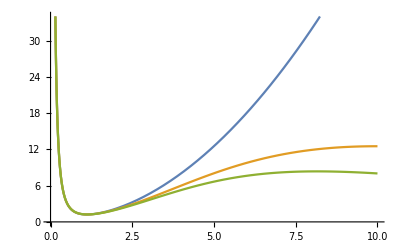

```mathematica
With[{m=1},
Plot[{Veff[m,0,r],Veff[m,0.01,r],Veff[m,0.015,r]},
{r,0.001,10}]]
```

```mathematica
Vf[m_, γ_, r_] := Veff[m, γ, r]*(f[γ, r])^2
```

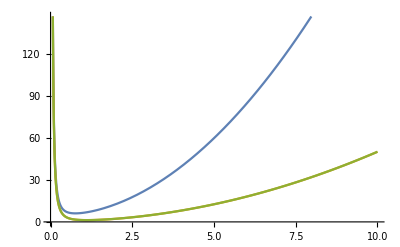

```mathematica
With[{m=1},
Plot[{Vf[m,1,r],Vf[m,0.01,r],Vf[m,0.015,r]},
{r,0.001,10}]]
```